```mathematica
(* Notebook created by F. Kopp , on 13/02/2018, any comments or sugestions send an email to fabio.kopp@ufrgs.br *)
Clear["Global`*"];
SetDirectory[NotebookDirectory[]]; 
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]; (* Package obtained from http://library.wolfram.com/infocenter/MathSource/6747/#downloads and created by Frank Rice
Organization:California Institute of Technology , Department:Physics *)
Needs["HypothesisTesting`"];
```

Importing the experimental data

```mathematica
sigtolexp=Import["sigtotalexp.dat","Table"];
dsigexp=Import["experimental-data.txt","Table"];
erroexp14=Transpose@{Flatten@dsigexp[[All,{1}]],Flatten@dsigexp[[All,{4}]]/(14.0^2),Flatten@dsigexp[[All,{5}]]/(14.0^2)};
erroexp22=Transpose@{Flatten@dsigexp[[All,{1}]],Flatten@dsigexp[[All,{7}]]/(22.0^2),Flatten@dsigexp[[All,{8}]]/(22.0^2)};
erroexp348=Transpose@{Flatten@dsigexp[[All,{1}]],Flatten@dsigexp[[All,{10}]]/(34.8^2),Flatten@dsigexp[[All,{11}]]/(34.8^2)};
erroexp383=Transpose@{Flatten@dsigexp[[All,{1}]],Flatten@dsigexp[[All,{13}]]/(38.3^2),Flatten@dsigexp[[All,{14}]]/(38.3^2^2)};
erroexp436=Transpose@{Flatten@dsigexp[[All,{1}]],Flatten@dsigexp[[All,{16}]]/(43.6^2),Flatten@dsigexp[[All,{17}]]/(43.6^2)};
```

Variables and constants of Bhabha process

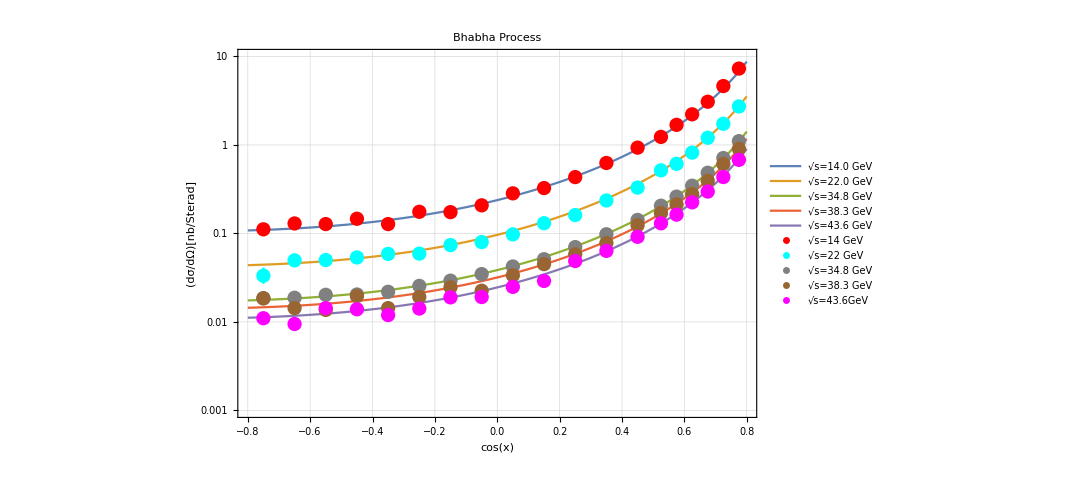

```mathematica
alpha=1.0/137.035;
d[s_,x_]:=((alpha^2)/(2*s^2))*((4+(1+x)^2)/(1-x)^2-(1+x)^2/(1-x)+(1+x^2)/2)*(0.389*10^6);
t1=ParallelTable[{x,d[14.0,x],d[22.0,x],d[34.8,x],d[38.3,x],d[43.6,x]},{x,-0.8,0.8,0.02}];
pl1=ListLogPlot[{t1[[All,{1,2}]],t1[[All,{1,3}]],t1[[All,{1,4}]],t1[[All,{1,5}]],t1[[All,{1,6}]]},Frame->True,FrameLabel->{"cos(x)","(dσ/dΩ)[nb/Sterad]"},PlotLegends->{"√s=14.0 GeV","√s=22.0 GeV","√s=34.8 GeV","√s=38.3 GeV","√s=43.6 GeV"},PlotStyle->Thick,PlotLabel->"Bhabha Process",ImageSize->800,Axes->False,GridLines->Automatic,Joined->True,PlotRange->{{-0.8,0.8},{0.001,10}}];
err14=ErrorListLogPlot[erroexp14, PlotStyle->Red,Frame->True,PlotLegends->{"√s=14 GeV"},Axes->False];
err22=ErrorListLogPlot[erroexp22, PlotStyle->Cyan,Frame->True,PlotLegends->{"√s=22 GeV"},Axes->False];
err34=ErrorListLogPlot[erroexp348, PlotStyle->Gray,Frame->True,PlotLegends->{"√s=34.8 GeV"},Axes->False];
err38=ErrorListLogPlot[erroexp383, PlotStyle->Brown,Frame->True,PlotLegends->{"√s=38.3 GeV"},Axes->False];
err43=ErrorListLogPlot[erroexp436, PlotStyle->Magenta,Frame->True,PlotLegends->{"√s=43.6GeV"},Axes->False];
Show[{pl1,err14,err22,err34,err38,err43}]
```

Total Cross Section (Integration over the solid angle )

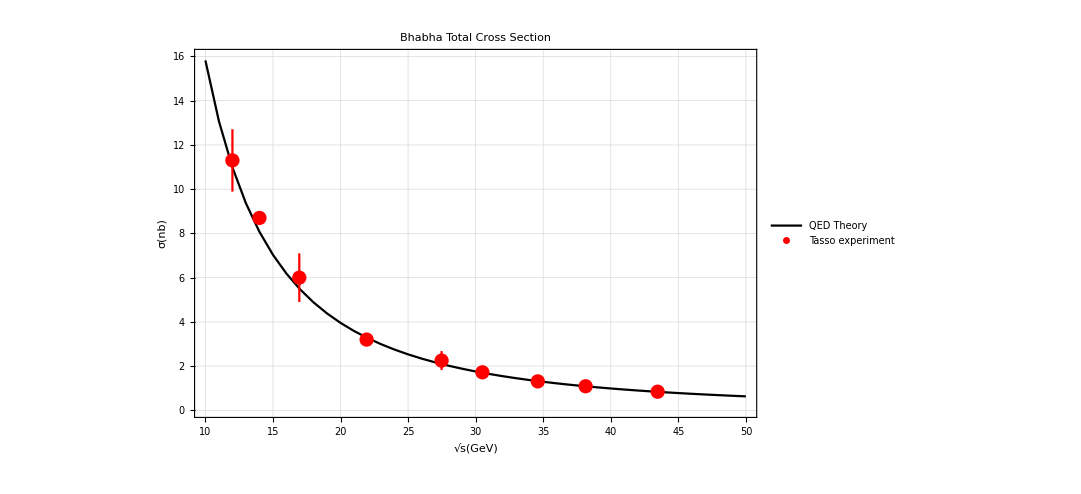

```mathematica
sig[s_]:=NIntegrate[{d[s,x]*Sqrt[1.0-(x^2)]*2.0*Pi},{x,-0.84,0.84},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}];
t2=ParallelTable[{s,sig[s][[1]]},{s,10,50}];
error=ErrorListPlot[sigtolexp, PlotStyle->Red,Frame->True,PlotLegends->{"Tasso experiment"}];
pl20=ListPlot[t2,Joined->True,PlotStyle->Black,Frame->True,PlotLegends->{"QED Theory"},PlotLabel->"Bhabha Total Cross Section",FrameLabel-> {Sqrt[s][GeV],σ[nb]},ImageSize->800,PlotRange->{{10,50},{0,16}},GridLines->Automatic];
plt=Show[ {pl20,error}]
```

Statistical Analysis

```mathematica
Chisquared[N0_,v0_,s0i2_]:=Module[{N=N0,v=v0,si2=s0i2},
s=si2^2;
ndf=(N-v);
For[i=1,i<Length[dsigexp[[All,1]]],i++,
x[i_]:=dsigexp[[i,1]] ;
y[i_]:=dsigexp[[i,10]]/s;
dy2[i_]:=Sqrt[(dsigexp[[i,11]]/s)^2];
yth[i_]:=d[si2,x[i]];
sol[i_]:= (( y[i]-yth[i])/dy2[i])^2];
chi=Sum[sol[i],{i,1,N}];
chired=chi/ndf;
pchi= ChiSquarePValue[chi,(N-v)][[2]];
Print["The chi-square is = ", chi];
Print["The chi-square reduced is = ", chired];
Print["The ndf are = ", ndf];
Print["The P(chi^2,ndf) probability is =  ",pchi];
];
```

Calculating the chi-square, chi-square reduced and P-chisquare probability

```mathematica
Np=19.0; (*Number of points *)
v=0.0;     (* Number of variables fitted to the model *)
s=34.8;  (*  s^1/2  energy of center of mass*)
```

```mathematica
Chisquared[Np,v,s]
```

The chi-square is = 23.9079

The chi-square reduced is = 1.25831

The ndf are = 19.

The P(chi^2,ndf) probability is =  0.199711